# xCellerator Example

ring-oscillator-enzymatic.nb

## A ring oscillator based on enzymatic reactions

Created: 02 August 2005 BES
Revised: 15 Oct 2007 Verify Under Mathematica 6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:47:55.898989 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

```mathematica
reactions={{Underoverscript[X⇄XP, ZPP, Z],a,d,k,a,d,k},
{Underoverscript[XP⇄XPP, ZPP, Z],a,d,k,a,d,k},{Underoverscript[Y⇄YP, XPP, X],a,d,k,a,d,k},{Underoverscript[YP⇄YPP, XPP, X],a,d,k,a,d,k},{Underoverscript[Z⇄ZP, YPP, Y],a,d,k,a,d,k},{Underoverscript[ZP⇄ZPP, YPP, Y],a,d,k,a,d,k}};
odes=interpret[reactions]
```

{{X'[t]==-a X[t] Y[t]-a X[t] YP[t]-a X[t] Z[t]+d Bind[X,Y][t]+k Bind[X,Y][t]+d Bind[X,YP][t]+k Bind[X,YP][t]+d Bind[X,Z][t]+k Bind[XP,ZPP][t],XP'[t]==-a XP[t] Z[t]-a XP[t] ZPP[t]+k Bind[X,Z][t]+d Bind[XP,Z][t]+d Bind[XP,ZPP][t]+k Bind[XPP,ZPP][t],XPP'[t]==-a XPP[t] YP[t]-a XPP[t] YPP[t]-a XPP[t] ZPP[t]+k Bind[XP,Z][t]+d Bind[XPP,YP][t]+k Bind[XPP,YP][t]+d Bind[XPP,YPP][t]+k Bind[XPP,YPP][t]+d Bind[XPP,ZPP][t],Y'[t]==-a X[t] Y[t]-a Y[t] Z[t]-a Y[t] ZP[t]+d Bind[X,Y][t]+k Bind[XPP,YP][t]+d Bind[Y,Z][t]+k Bind[Y,Z][t]+d Bind[Y,ZP][t]+k Bind[Y,ZP][t],YP'[t]==-a X[t] YP[t]-a XPP[t] YP[t]+k Bind[X,Y][t]+d Bind[X,YP][t]+d Bind[XPP,YP][t]+k Bind[XPP,YPP][t],YPP'[t]==-a XPP[t] YPP[t]-a YPP[t] ZP[t]-a YPP[t] ZPP[t]+k Bind[X,YP][t]+d Bind[XPP,YPP][t]+d Bind[YPP,ZP][t]+k Bind[YPP,ZP][t]+d Bind[YPP,ZPP][t]+k Bind[YPP,ZPP][t],Z'[t]==-a X[t] Z[t]-a XP[t] Z[t]-a Y[t] Z[t]+d Bind[X,Z][t]+k Bind[X,Z][t]+d Bind[XP,Z][t]+k Bind[XP,Z][t]+d Bind[Y,Z][t]+k Bind[YPP,ZP][t],ZP'[t]==-a Y[t] ZP[t]-a YPP[t] ZP[t]+k Bind[Y,Z][t]+d Bind[Y,ZP][t]+d Bind[YPP,ZP][t]+k Bind[YPP,ZPP][t],ZPP'[t]==-a XP[t] ZPP[t]-a XPP[t] ZPP[t]-a YPP[t] ZPP[t]+d Bind[XP,ZPP][t]+k Bind[XP,ZPP][t]+d Bind[XPP,ZPP][t]+k Bind[XPP,ZPP][t]+k Bind[Y,ZP][t]+d Bind[YPP,ZPP][t],Bind[X,Y]'[t]==a X[t] Y[t]-d Bind[X,Y][t]-k Bind[X,Y][t],Bind[X,YP]'[t]==a X[t] YP[t]-d Bind[X,YP][t]-k Bind[X,YP][t],Bind[X,Z]'[t]==a X[t] Z[t]-d Bind[X,Z][t]-k Bind[X,Z][t],Bind[XP,Z]'[t]==a XP[t] Z[t]-d Bind[XP,Z][t]-k Bind[XP,Z][t],Bind[XP,ZPP]'[t]==a XP[t] ZPP[t]-d Bind[XP,ZPP][t]-k Bind[XP,ZPP][t],Bind[XPP,YP]'[t]==a XPP[t] YP[t]-d Bind[XPP,YP][t]-k Bind[XPP,YP][t],Bind[XPP,YPP]'[t]==a XPP[t] YPP[t]-d Bind[XPP,YPP][t]-k Bind[XPP,YPP][t],Bind[XPP,ZPP]'[t]==a XPP[t] ZPP[t]-d Bind[XPP,ZPP][t]-k Bind[XPP,ZPP][t],Bind[Y,Z]'[t]==a Y[t] Z[t]-d Bind[Y,Z][t]-k Bind[Y,Z][t],Bind[Y,ZP]'[t]==a Y[t] ZP[t]-d Bind[Y,ZP][t]-k Bind[Y,ZP][t],Bind[YPP,ZP]'[t]==a YPP[t] ZP[t]-d Bind[YPP,ZP][t]-k Bind[YPP,ZP][t],Bind[YPP,ZPP]'[t]==a YPP[t] ZPP[t]-d Bind[YPP,ZPP][t]-k Bind[YPP,ZPP][t]},{X,XP,XPP,Y,YP,YPP,Z,ZP,ZPP,Bind[X,Y],Bind[X,YP],Bind[X,Z],Bind[XP,Z],Bind[XP,ZPP],Bind[XPP,YP],Bind[XPP,YPP],Bind[XPP,ZPP],Bind[Y,Z],Bind[Y,ZP],Bind[YPP,ZP],Bind[YPP,ZPP]}}

```mathematica
r=run[odes, initialConditions-> {X-> 1, Y-> 1.5, Z-> 2}, rates-> {a-> 1, d-> 1, k-> 1}]
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,XPP,YP,YPP,ZP,ZPP,Bind[X,Y],Bind[X,YP],Bind[X,Z],Bind[XP,Z],Bind[XP,ZPP],Bind[XPP,YP],Bind[XPP,YPP],Bind[XPP,ZPP],Bind[Y,Z],Bind[Y,ZP],Bind[YPP,ZP],Bind[YPP,ZPP]}

{{X→InterpolatingFunction[{{0.,100.}},<>],XP→InterpolatingFunction[{{0.,100.}},<>],XPP→InterpolatingFunction[{{0.,100.}},<>],Y→InterpolatingFunction[{{0.,100.}},<>],YP→InterpolatingFunction[{{0.,100.}},<>],YPP→InterpolatingFunction[{{0.,100.}},<>],Z→InterpolatingFunction[{{0.,100.}},<>],ZP→InterpolatingFunction[{{0.,100.}},<>],ZPP→InterpolatingFunction[{{0.,100.}},<>],Bind[X,Y]→InterpolatingFunction[{{0.,100.}},<>],Bind[X,YP]→InterpolatingFunction[{{0.,100.}},<>],Bind[X,Z]→InterpolatingFunction[{{0.,100.}},<>],Bind[XP,Z]→InterpolatingFunction[{{0.,100.}},<>],Bind[XP,ZPP]→InterpolatingFunction[{{0.,100.}},<>],Bind[XPP,YP]→InterpolatingFunction[{{0.,100.}},<>],Bind[XPP,YPP]→InterpolatingFunction[{{0.,100.}},<>],Bind[XPP,ZPP]→InterpolatingFunction[{{0.,100.}},<>],Bind[Y,Z]→InterpolatingFunction[{{0.,100.}},<>],Bind[Y,ZP]→InterpolatingFunction[{{0.,100.}},<>],Bind[YPP,ZP]→InterpolatingFunction[{{0.,100.}},<>],Bind[YPP,ZPP]→InterpolatingFunction[{{0.,100.}},<>]}}

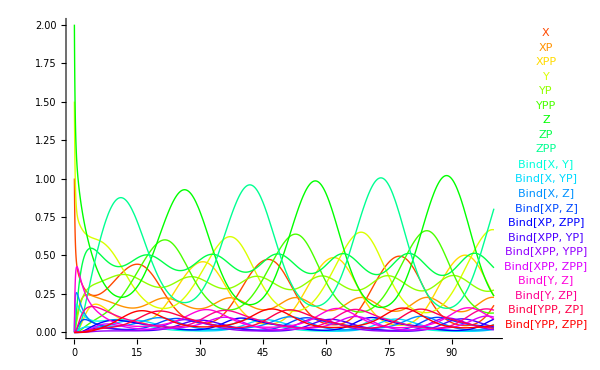

```mathematica
runPlot[r,PlotRange-> All, ImageSize-> 600]
```

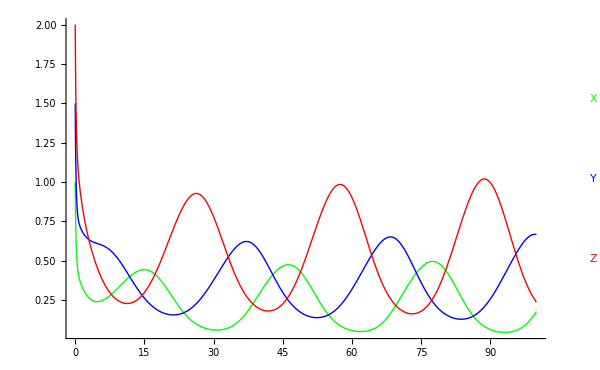

```mathematica
runPlot[r,{X,Y,Z},PlotRange-> All, ImageSize-> 600]
```

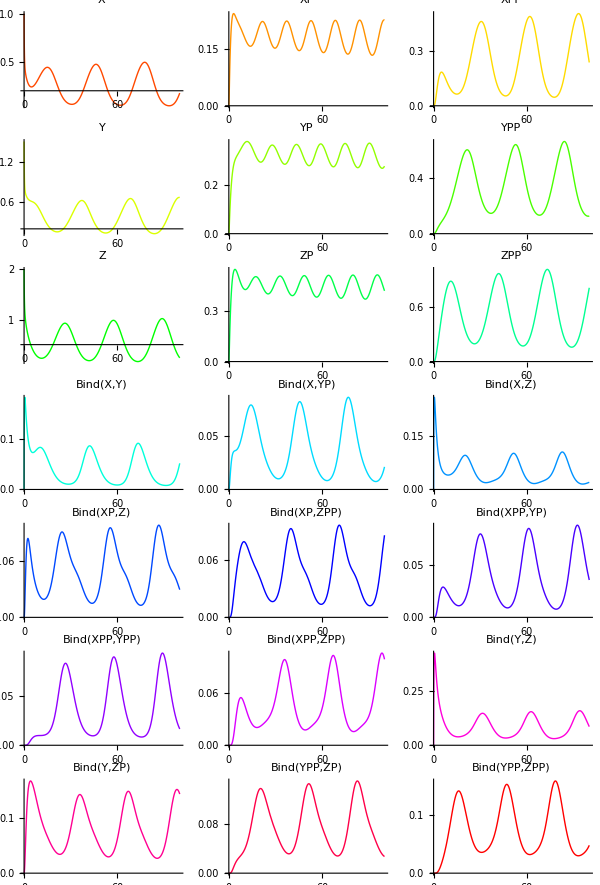

```mathematica
gridPlot[r, All, {0,100}, plotColumns-> 3, ImageSize-> 600]
```